# Random variate generation/Importance sampling using integral transforms

Eugene d’Eon
NVIDIA
Wellington, New Zealand
April 5, 2020

### Abstract

We discuss various analytic and exact methods for deriving importance-sampling procedures for 1D distributions f(r) on the half line r ∈ [0,∞).  Specifically:

Finding convolutions using the forward Laplace transform

Sampling as a superposition of exponentials using the inverse Laplace transform

The Gaussian transform

Generalized Box-Muller projections

Sampling using a track-length estimator

## 1. Introduction

Simulating the linear transport of light or particles often involves drawing random variates from some given distribution on the half line, such as free-path length sampling in homogeneous classical media where we draw samples from the collision-rate density σ_t e^(-σ_t r) using the CDF inversion method, leading to

```mathematica
r=-Log[1-RandomReal[]]/Subscript[σ, t].
```

There are times where we wish to sample other distributions f(r) on the half line where the CDF inversion method is not possible analytically.  For example, in non-classical transport where free-path lengths between collision are not exponentially-distributed, we need sampling procedures for a large class of distributions that give the chord-lengths in a given class of random microstructure.

In this paper we discuss methods for sampling from a 1D distribution f(r) that is normalized on the half line ∫_0^∞ f(r)ⅆr = 1.  In most cases, more than 1 random number will be required to sample f(r).

## 2. Deconvolution

If f(r) can be expressed as a convolution of more than 1 distribution, each of which has known sampling procedures, then f(r) can be sampled as a whole by sampling each of the distributions in its convolution and summing the values r_i.  The Laplace transform can be used to factor f(r) into its deconvolved components using the convolution property of Laplace transforms: the Laplace transform of a convolution is the product of the two Laplace transforms,  ℒ_r[f_1(r) ⋆ f_2(r) ](s)= ℒ_r[f_1(r)](s)  ℒ_r[f_2(r)](s).

### Example 2.1:

Consider the Erlang-2 / Gamma-2 distribution, f(r) = e^-r r.

```mathematica
Clear[f];
f[r_]:=Exp[-r]r;
 Integrate[f[r],{r,0,Infinity}]
```

1

We can’t analytically invert the CDF of f(r):

```mathematica
Integrate[f[r],{r,0,k},Assumptions->k>0]
```

1-ⅇ^-k (1+k)

Using the Laplace transform of f(r):

```mathematica
LaplaceTransform[f[r],r,s]
```

1/(1+s)^2

we note that f is the convolution of a function with itself, whose laplace transform is 1/(1+s).  Using the inverse Laplace transform, we find

```mathematica
InverseLaplaceTransform[1/(1+s),s,r]
```

ⅇ^-r

We find the exponential, which we know how to sample.  Therefore, Erlang-2 can be sampled using the sum of 2 calls to sample() procedure for the exponential:

```mathematica
sampleExp[]:=-Log[RandomReal[]];
```

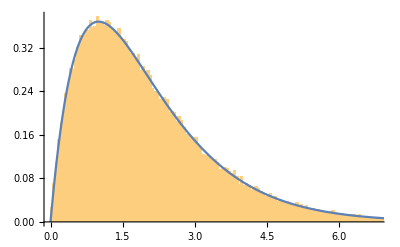

```mathematica
Show[
Histogram[
Table[sampleExp[]+sampleExp[],{i,Range[100000]}],200,"PDF"],
Plot[f[r],{r,0,7},PlotRange->All]
]
```

In general the Gamma distribution f(r) = e^-r r^(a-1)/Gamma[a] can be sampled as the sum of a exponential random variates.  In the case of non-integer a, Marsaglia's method can be used.

## 3. Discrete Decomposition

Sometimes f(r) can be written as the sum of several non-negative distributions f(r) = ∑_(i=1)^n w_i f_i(r), each of which is normalized ∫_0^∞ f_i(r)ⅆr = 1 and an analytic sampling procedure is known for each f_i(r).  In this case, one random number can be used to first select one of the f_i distributions using a CDF built from the weights w_i, and then a second independent random number can be used to sample f_i.  The resulting distance r is then distributed by f(r).

## 4. Continuous superpositions

A continuous generalization of the previous discrete decomposition is when f(r) can be expressed as a continuous superposition of a family of distributions g(r,s), where an exact analytic sampling procedure for g(r,s) is known: f(r) = ∫_0^∞ g(r,s)w(s)ⅆs, where s is a parameter for distribution g (such as the mean of g) and w(s) ≥ 0, for s ≥ 0.  If a sampling procedure is also known for w(s), then we can first sample s from w, and then sample g(r,s) with the sampled s parameter value.

### Example 4.1 - BesselK_0

Consider the distribution 2/π K_0(r):

```mathematica
Clear[f];
f[r_]:=2/Pi BesselK[0,r];
Integrate[f[r],{r,0,Infinity}]
```

1

We can write f(r) as the superposition of exponentials:

```mathematica
w[s_]:=2/(π  s √(-1+s^2))HeavisideTheta[s-1]
```

```mathematica
Integrate[w[s] s Exp[-s r],{s,0,Infinity},Assumptions->r>0]
```

(2 BesselK[0,r])/π

We check to see we can sample inverse mfp s from w(s).  The CDF of the weight function w(s) is

```mathematica
Integrate[w[s],{s,1,S},Assumptions->S>1]
```

(2 ArcSec[S])/π

which we can invert

```mathematica
Solve[ξ==(2 ArcSec[S])/π,S]
```

{{S→ConditionalExpression[Sec[(π ξ)/2],(ξ≠1&&0<π Re[ξ]<2 π)||(π Re[ξ]==0&&π Im[ξ]≥0)||(π Re[ξ]==2 π&&π Im[ξ]≤0)]}}

So we can sample inverse mfp s using Sec[(π ξ_1)/2] where ξ_1 is a uniform random real in [0,1], and then sample the exponential using:  -log(ξ_2)/s:

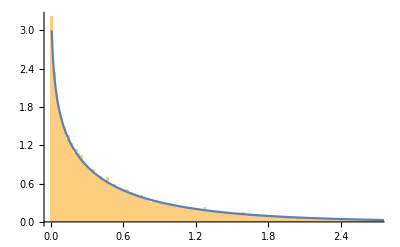

```mathematica
Show[
Histogram[Table[(-Log[RandomReal[]]/Sec[(π RandomReal[])/2]),{i,Range[50000]}],450,"PDF"],
Plot[f[r],{r,0,10},PlotRange->{0,3}]
]
```

## 5. Finding continuous superpositions of a given f(r)

### When the inverse Laplace transform ℒ_r^-1[f(r)](s) is known (superposition of exponentials)

When the inverse Laplace transform ℒ_r^-1[f(r)](s) of f(r) is known, then a weight function for a superposition of exponentials s e^(-s r) is w(s) = (ℒ_r^-1[f(r)](s))/s.  If w(s) can be sampled, then we have a new 2-random-number sampling procedure for f(r).

#### Example 5.1:

Consider the distribution f(r) given by:

```mathematica
f[r_]:=√(2/π)-ⅇ^(r^2/2) r Erfc[r/(√2)]
```

We check the inverse Laplace:

```mathematica
1/s FullSimplify[InverseLaplaceTransform[f[r],r,s],Assumptions->s>0]
```

ⅇ^(-s^2/2) √(2/π)

This is a weighting function w(s), which is simply a Gaussian/Normal distribution, which is easily sampled.

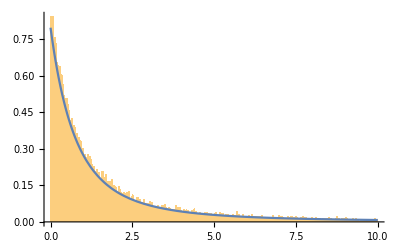

```mathematica
Show[
Histogram[
Table[(-Log[RandomReal[]])/Abs[RandomVariate[NormalDistribution[]]],{i,Range[30000]}],{0,10,0.03},"PDF"],
Plot[f[r],{r,0,10},PlotRange->All]
]
```

### When the inverse Laplace transform ℒ_r^-1[f(√r)](s) is known (superpositions of Gaussians)

Sometimes the inverse Laplace transform of f(r) is not known but the inverse Laplace transform of f(√r) is.  In this case, it may be possible to sample f(r) using the Gaussian (or Normal) distribution.  To do this, use the Gaussian transform, described next.

## 6. The Gaussian Transform

The 1D Gaussian/Normal distribution on the half line with variance s is:

```mathematica
Gaussian[r_,s_]:=2/(√(2 Pi s))Exp[-r^2/(2 s)]
```

and is normalized on the half line:

```mathematica
Integrate[Gaussian[r,s],{r,0,Infinity},Assumptions->s>0]
```

1

This one-sided Gaussian/Normal distribution can be sampled using inverseErf[] or the Box-Muller algorithm.

The Gaussian transform [Alecu et al. 2006] can be used to solve for a weight function w[s] such that f(r) can be expressed as a superposition of Gaussians: f(r) = ∫_0^∞ Gaussian(r,s)w(s)ⅆs.

### Example 6.1 - w[s] is Erlang-2/Gamma-2:

```mathematica
w[s_]:=Exp[-s]s
```

```mathematica
Integrate[w[s],{s,0,Infinity}]
```

1

Find f(r) given w(s) as the weighting function of Gaussians:

```mathematica
f=Integrate[w[s]Gaussian[r,s],{s,0,Infinity},Assumptions->r>0]
```

(ⅇ^(-√2 r) (1+√2 r))/(√2)

Try the Gaussian transform to find w(s) given f(r):

```mathematica
1/(2 s)√(Pi/(2s))InverseLaplaceTransform[f/.r->√r,r,t]/.t->1/(2 s)
```

ⅇ^-s s

### Example 6.2 - BesselK_0

```mathematica
w[s_]:=(Exp[-s] s^(-1/2))/(√Pi)
```

```mathematica
Integrate[w[s],{s,0,Infinity}]
```

1

Find f(r) given w(s) as the weighting function of Gaussians:

```mathematica
f=Integrate[w[s]Gaussian[r,s],{s,0,Infinity},Assumptions->r>0]
```

(2 √2 BesselK[0,√2 r])/π

Try the Gaussian transform to find w(s) given f(r):

```mathematica
1/(2 s)√(Pi/(2s))InverseLaplaceTransform[f/.r->√r,r,t]/.t->1/(2 s)
```

(ⅇ^-s √(1/s))/(√π)

### Example 6.3

```mathematica
w[s_]:=1/(1+s)
```

Find f(r) given w(s) as the weighting function of Gaussians:

```mathematica
f=Integrate[w[s]Gaussian[r,s],{s,0,Infinity},Assumptions->r>0]
```

ⅇ^(r^2/2) √(2 π) Erfc[r/(√2)]

Try the Gaussian transform to find w(s) given f(r):

```mathematica
1/(2 s)√(Pi/(2s))InverseLaplaceTransform[f/.r->√r,r,t]/.t->1/(2 s)//Simplify
```

1/(1+s)

### Example 6.4

```mathematica
w[s_]:=1/(s(1+s))
```

Find f(r) given w(s) as the weighting function of Gaussians:

```mathematica
f=Integrate[w[s]Gaussian[r,s],{s,0,Infinity},Assumptions->r>0]
```

2/r-ⅇ^(r^2/2) √(2 π) Erfc[r/(√2)]

Try the Gaussian transform to find w(s) given f(r):

```mathematica
1/(2 s)√(Pi/(2s))InverseLaplaceTransform[f/.r->√r,r,t]/.t->1/(2 s)//Simplify
```

1/(s+s^2)

### Example 6.5: Cauchy superposition of Gaussians

```mathematica
w[s_]:=1/(1+s^2)2/Pi
```

```mathematica
Integrate[w[s],{s,0,Infinity}]
```

1

Find f(r) given w(s) as the weighting function of Gaussians:

```mathematica
f=Integrate[w[s]Gaussian[r,s],{s,0,Infinity},Assumptions->r>0]
```

(2 (π Cos[r^2/2] (1-2 FresnelC[r/(√π)])+π (1-2 FresnelS[r/(√π)]) Sin[r^2/2]))/π^(3/2)

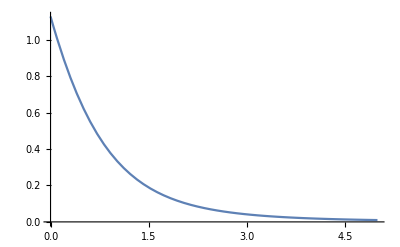

```mathematica
Plot[(2 (π Cos[r^2/2] (1-2 FresnelC[r/(√π)])+π (1-2 FresnelS[r/(√π)]) Sin[r^2/2]))/π^(3/2),{r,0,5}]
```

Try the Gaussian transform to find w(s) given f(r):

```mathematica
1/(2 s)√(Pi/(2s))InverseLaplaceTransform[f/.r->√r,r,t]/.t->1/(2 s)//Simplify
```

((1/s)^(3/2) InverseLaplaceTransform[π Cos[r/2] (1-2 FresnelC[(√r)/(√π)])+π (1-2 FresnelS[(√r)/(√π)]) Sin[r/2],r,1/(2 s)])/(√2 π)

Mathematica is not always able to find it.

## 7. Generalized Box-Muller

We now show how to solve for isotropic random flights in d dimension that project onto a single axis to give some desired symmetric distribution.  We need the surface area of the sphere of radius r in dD:

```mathematica
SA[d_,r_]:=d Pi^(d/2)/Gamma[d/2+1] r^(d-1)
```

and the inverse Fourier/Hankel transform in dD [Dutka 1985]

```mathematica
inv[d_,f_]:=r^(1-d/2)(2Pi)^(-d/2)Integrate[z^(d/2)BesselJ[d/2-1,z r]f,{z,0,Infinity},Assumptions->d≥1&&r>0&&assumps]
```

Given a desired distribution f(r) on the half line we wish to sample, we first form the Fourier transform

```mathematica
F=√(2Pi)FourierTransform[1/2 f[Abs[r]],r,z]
```

and then search for some dimension d such that the inverse Hankel transform

```mathematica
p=inv[d,F]SA[d,r]
```

gives a distribution p(r) that we can sample analytically.  If so, then sampling a random isotropic direction in dD, and then a random step from p(r), and projecting onto a single axis, and taking the abs(x), gives a sample procedure for f(r).

### Example 7.1 - Box Muller sampling of the Gaussian

Suppose we wish to sample a random variate from a one-sided Gaussian/Normal distribution

```mathematica
f[r_]:=Gaussian[r,1]
```

```mathematica
f[r]
```

ⅇ^(-r^2/2) √(2/π)

```mathematica
Integrate[f[r],{r,0,Infinity}]
```

1

Following the 2 steps above, and knowing that the Box-Muller transform works in Flatland, d = 2, we find

```mathematica
F=√(2Pi)FourierTransform[1/2 f[Abs[r]],r,z]
```

ⅇ^(-z^2/2)

```mathematica
p=inv[2,F]SA[2,r]
```

ⅇ^(-r^2/2) r

We find that a single-step random flight in 2D with an isotropic starting direction and free-path length drawn from ⅇ^(-r^2/2) r will produce a Gaussian random number when projected onto one axis.  Sampling p by CDF inverse leads to:

```mathematica
Integrate[ⅇ^(-r^2/2) r,{r,0,R},Assumptions->R>0]
```

1-ⅇ^(-R^2/2)

```mathematica
Solve[1-ⅇ^(-R^2/2)==xi,R]
```

{{R→ConditionalExpression[-√2 √(2 ⅈ π C[1]+Log[1/(1-xi)]),C[1]∈ℤ]},{R→ConditionalExpression[√2 √(2 ⅈ π C[1]+Log[1/(1-xi)]),C[1]∈ℤ]}}

And so we sample a radius using √2 √Log[1/(1-xi)]

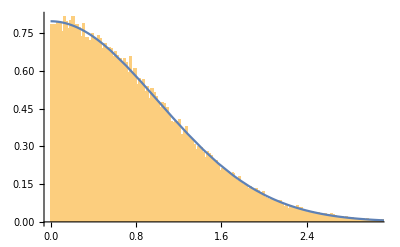

```mathematica
Show[
Histogram[
Table[Abs[√2 √Log[1/(1-RandomReal[])] Cos[2 Pi RandomReal[]]],{i,Range[100000]}],200,"PDF"],
Plot[f[r],{r,0,7},PlotRange->All]
]
```

### Example 7.2 - Sampling GGX distribution of visible normals

In sampling the distribution of visible normals for the GGX normal distribution the following distribution requires sampling [Heitz and d’Eon 2014] in order to sample slope q conditioned on having sampled slope p:

```mathematica
f[q_]:=(2/(π (1+q^2)^2)).
```

This was sampled using an approximate inverse in [Heitz and d’Eon 2014] and later an exact scheme was provided [Heitz 2018].  However, the generalized Box-Muller approach in 2D also works.  We find (using a variant for f(q) on the full line):

```mathematica
F=√(2Pi)FourierTransform[f[Abs[r]],r,z]
```

ⅇ^(-Abs[z]) (1+Abs[z])

```mathematica
p=inv[2,F]SA[2,r]
```

(3 r)/((1+r^2)^(5/2))

This distribution is easily sampled

```mathematica
Integrate[(3 r)/((1+r^2)^(5/2)),{r,0,R},Assumptions->R>0]
```

1-1/((1+R^2)^(3/2))

```mathematica
Solve[xi==1-1/((1+R^2)^(3/2)),R]
```

{{R→-√(-1+1/(1-xi)^(2/3))},{R→√(-1+1/(1-xi)^(2/3))}}

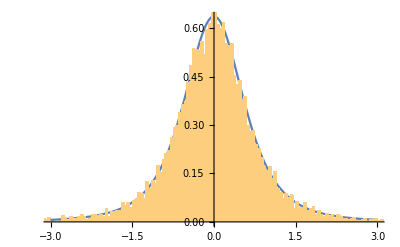

```mathematica
Show[
Plot[f[q] ,{q,-3,3}],
Histogram[
Table[
Sin[2 Pi RandomReal[]] √(-1+1/(1-RandomReal[])^(2/3))
,{i,Range[10000]}]
,500,"PDF"]
]
```

## 8. Combining various techniques

We consider here an example that combines several of the above techniques to sample the distribution of visible normals for GGX by using the exact sampling method for Beckmann.  This is far less efficient than known sampling procedures for the GGX vNDF sampling [Heitz 2018].  However, the procedure highlights several of the above approaches.  Based on the observation that GGX is simply a superposition of Beckmanns:

```mathematica
DBeckmann[u_,α_]:=1/(Pi α^2 (u)^4)E^(-((1/(u)^2-1)/α^2))
```

```mathematica
DGGX[u_,α_]:=(α^2 1/(u)^4)/(π (α^2+(1/(u)^2-1))^2)
```

```mathematica
Integrate[(2 ⅇ^(-GGXm^2/m^2) GGXm^2)/m^3 DBeckmann[u,m],{m,0,Infinity},Assumptions->GGXm>0&&0<u<1]-DGGX[u,GGXm]//FullSimplify
```

0

we find that the GGX vNDF can be sampled using an exact vNDF procedure for Beckmann [Heitz and d’Eon 2014] by first sampling Beckmann roughness m’ from:

```mathematica
mprime[m_,u_]:=-(ⅇ^(m/(-1+u^2)) (-1+u))/(√π √(m-m u^2))+(ⅇ^-m u (1+Erf[u √(-m/(-1+u^2))]))/(1+u)
```

where u = cos θ_i and m is the roughness of the desired GGX NDF.  To sample the m'(m) distribution we consider:

```mathematica
LaplaceTransform[mprime[m,u],m,s]
```

u/((1+s) (1+u))+u/((1+s) √(1+(1+s) (-1+1/u^2)) (1+u))-(-1+u)/(√(1+s-s u^2))

We separate this into 3 components m̄(s) = m1(s) + m2(s) + m3(s):

```mathematica
m1[s_]:=u/(1+u)1/(1+s)
```

We recognize this as an exponential distribution from 1/(1+s).  The second term can simplify,

```mathematica
FullSimplify[u/(√(1+(1+s) (-1+1/u^2)) (1+u)),Assumptions->s>0&&0<u<1]
```

u^2/((1+u) √(1+s-s u^2))

```mathematica
m2[s_]:=u^2/(1+u)1/(1+s)1/(√(1+s-s u^2))
```

We recognize this as the convolution of an exponential 1/(1+s) with a new distribution 1/(√(1+s-s u^2)), which also appears in the third term:

```mathematica
m3[s_]:=(1-u)1/(√(1+s-s u^2))
```

We now have three terms.  Their selection weights are found from s = 0,

```mathematica
{m1[s],m2[s],m3[s]}/.s->0
```

{u/(1+u),u^2/(1+u),1-u}

Which we verify sum to 1:

```mathematica
%//Total//FullSimplify
```

1

We just need to find a sampling procedure for the inverse Laplace transform of 1/(√(1+s-s u^2)),

```mathematica
InverseLaplaceTransform[1/(√(1+s-s u^2)),s,r]
```

(ⅇ^(-r/(1-u^2)))/(√π √r √(1-u^2))

Try CDF inversion,

```mathematica
FullSimplify[Integrate[(ⅇ^(-r/(1-u^2)))/(√π √r √(1-u^2)),{r,0,R},Assumptions->R>0],Assumptions->0<u<1&&R>0]
```

Erf[√(-R/(-1+u^2))]

```mathematica
Solve[xi==Erf[√(-R/(-1+u^2))],R]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{R→-(-1+u^2) InverseErf[xi]^2}}

We can sample m2 and m3 using this, assuming we have an efficient InverseErf(),

```mathematica
samplemprime[u_]:=Module[{xi1},
xi1=RandomReal[]; (* term selection variable *)
If[xi1<u/(1+u),
-Log[RandomReal[]] (* sample m1(s) *)
,
If[xi1<u/(1+u)+(1-u),
-(-1+u^2) InverseErf[RandomReal[]]^2 (* sample m3 *)
,
-Log[RandomReal[]]-(-1+u^2) InverseErf[RandomReal[]]^2  (* sample m2 - by convolution *)
]
]
]
```

Verify our derivation:

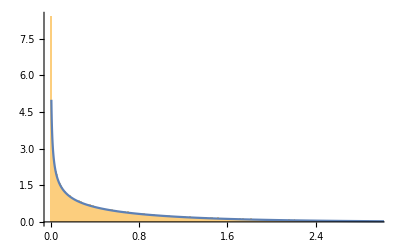

```mathematica
With[{u=0.3},
Show[
Histogram[Table[samplemprime[u],{i,Range[100000]}
],1300,"PDF"],
Plot[mprime[m,u],{m,0,5},PlotRange->{0,5}]

]
]
```

## 9. Track-length estimators

In the case that a track-length estimator [Heitz and Belcour 2018] is used to sample f(r) by scoring at all positions in [0,r] when distance r is sampled, we note that the r can be sampled as a superposition of exponentials by sampling inverse mfp s  from ℒ_r^-1[f(r)](s) as opposed to (ℒ_r^-1[f(r)](s))/s for standard sampling, which follows from the property of the Laplace transform of the integral of a function f(r).

### Example 9.1:

Suppose we want to sample f(r) using a track-length estimator where f(r) is given as:

```mathematica
f[r_]:=1+r+ⅇ^r r (2+r) ExpIntegralEi[-r]
```

```mathematica
Integrate[f[r],{r,0,Infinity}]
```

1

Knowing that f(r) is given by a Laplace transform (contrived example)

```mathematica
LaplaceTransform[(2s)/(1+s)^3,s,r]//FullSimplify
```

1+r+ⅇ^r r (2+r) ExpIntegralEi[-r]

We can sample s from (2s)/(1+s)^3 and then r from s e^(-r s) and the track-length estimator will sample f(r).

CDF sampling of (2s)/(1+s)^3 yields

```mathematica
Solve[xi==Integrate[(2 s)/(1+s)^3,{s,0,S},Assumptions->S>0],S]
```

{{S→(-√xi-xi)/(-1+xi)},{S→(√xi-xi)/(-1+xi)}}

Verify that a track-length estimator samples f(r):

```mathematica
tls=Sum[HeavisideTheta[#-t]&[-Log[RandomReal[]]/((-√#-#)/(-1+#)&[RandomReal[]])],{i,Range[700]}]/700;
```

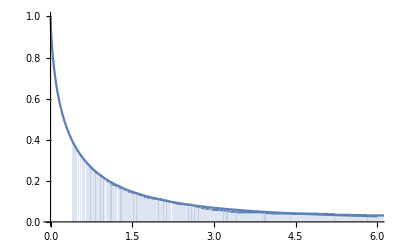

```mathematica
Show[
Plot[f[t],{t,0,6},PlotRange->{0,1}],
Plot[tls,{t,0,16},Filling->Axis,PlotRange->{0,1}]
]
```

## 10. References

Alecu et al. 2006 - The Gaussian Transform of Distributions: Definition, Computation and Application.  IEEE TRANSACTIONS ON SIGNAL PROCESSING, VOL. 54, NO. 8, AUGUST 2006.  doi: 10.1109/TSP.2006.877657

Heitz, E. and d’Eon, E. 2014 - Importance sampling microfacet-based BSDFs using the distribution of visible normals. In Proceedings of the 25th Eurographics Symposium on Rendering, Eurographics Association, Aire-la-Ville, Switzerland, EGSR ’14, 103–112. URL: https://hal.inria.fr/hal-00996995v2.

Heitz and Belcour 2018 - A note on track-length sampling with non-exponential distributions.  https://hal.inria.fr/hal-01788593v1

Heitz, E. 2018 - Sampling the GGX Distribution of Visible Normals, JCGT.  http://jcgt.org/published/0007/04/01/